# High Level Language

High level programming languages, such as C, Java, Ruby, Python, and Mathematica, are designed for manipulating abstract data types, and create concrete computational results that is easy for human consumption. Since this note is designed to work with the Nand2X course, we will talk about building an application using high level language features.

## Learning by Applying

This chapter, we will look at a few examples of using Mathematica’s built-in functions to create animation or simple interactive applications. The experience of developing these simple application will give you some sense of what high level programming languages can do. More importantly, it will give you an idea of how to think about developing a system from a functional programming approach. Once you learned the pattern of how to compose a set of functions to perform the task, then, you will have a better sense to develop the compiler for the high level language.

App Examples

At the same time, we will also show you some simple applications written in a few lines of Mathematica code. Having this observation will give you a better idea of how to go about designing the compiler of the language. This is an interesting teaching strategy set out by Noam Nisan and Shimon Shocken in their book. We will follow their strategy here.

## Some Simple Applications

In this part, I try to collect some very simple applications, so that you can see that the concern of building an application is not just about computation. Some of your concern will be related to human-machine interfaces. That means you will have to learn a vocabulary that would drive you away from thinking about just the behavior of the computer, but also the interactive interfaces between users and the computing program.

Dynamics in Mathematica

Dynamic[...] as a function is a very special member in the language. This function provides a marker, indicating that the expressions wrapped around by “Dynamic” will be updated when ever some new events take place. Let’s try it out:

```mathematica
result =Dynamic[x^2]
```

The previous line should have an output showing that “result” should be x^2, but when the next line sets x to be 3, the previous output cell will become the new value by supplying the new value of x. This is important, because this provides a brand new mechanism to update values in the name space of Mathematica’s runtime system. Sometimes, this can be very dangerous. That is partially why Mathematica becomes fairly unstable after Dynamics and Manipulate became a dominant part of Notebook code since Mathematica 6.0.

```mathematica
Clear[x]
```

```mathematica
x=3
```

3

```mathematica
c =Dynamic[x*2]
```

Working with Control Objects

Given this new dynamically updated name scope, we have the following situation.

```mathematica
Slider[Dynamic[x]]
```

One may tell, as you change the slider value, the value of x is being updated, and all parts of Notebook that uses Dynamic as a marker to bind its values to x, will be updated as x get updates from the control object.

## Control Objects

This following example shows that you can treat function as a variable, and use Manipulate function and a list of function names to perform interactions.

```mathematica
Manipulate[Plot[f[c x],{x,-10,10}],{f,{Sin, Cos, Tan, Sinh,Cosh, Tanh}, SetterBar},
{c,1,10}]
```

```mathematica
Manipulate[Plot[f[c x],{x,-10,10}],{f,{Sin, Cos, Tan, Sinh,Cosh, Tanh}, RadioButtonBar},
{c,1,10}]
```

```mathematica
Manipulate[Plot[f[c x],{x,-10,10}],{f,{Sin, Cos, Tan, Sinh,Cosh, Tanh}, RadioButtonBar},
{c,1,10}, ControlPlacement->VerticalSlider]
```

```mathematica
Manipulate[Plot[Sin[c x],{x,-10,10}],
{c,1,10}, ControlPlacement->VerticalSlider]
```

User Interface Components

As you might already noticed, Mathematica provides a number of human-machine interface components to minimize your coding labor. This is exactly what I want you to notice. The point of learning about programming, is the identify what kind of infrastructures that have already been provided to you. The focus shouldn’t be doing everything yourself, but to learn about what are the industrialized practices.

NetLogo and Mathematica

Similar to NetLogo, Mathematica’s Dynamic Interface, especially the Manipulate function, already provides a cookie cutter function for you to compose new functions. That means, building an app is not about writing everything from scratch. NetLogo and Processing, and even Arduino programming environment, provides you with a pre-built set of iterators. These iterators provides a standard notion of time, so that as the dynamic interface proceeds in its global timer, it drives all the relevant parameters and calls the time-increment function every time it changes the value of global time.

## 2016 One Liner Competition Entries:

```mathematica
CountryData["World", {"Shape",#}]⟦1,3,1⟧&/@{"Orthographic", "Mercator"};
Animate[Graphics[{Polygon[%⟦1⟧+f(%⟦2⟧-%⟦1⟧)]}],{f,0,.04}]
```

# Special Data Types

## Graph Structure

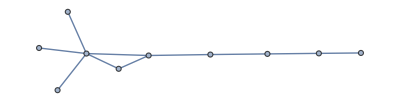

```mathematica
randomGraph =RandomGraph[{10,10}]
```

```mathematica
Manipulate[RandomGraph[{a,b}],{a,1,10,1},{b,1,100,1}]
```

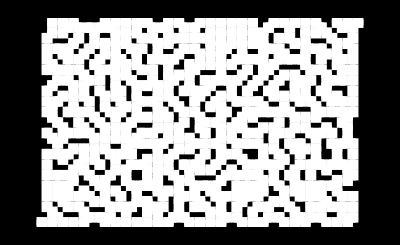
```mathematica
maze=-Graphics-;
```